# Fault Tolerance

In Notebook 9.2 we demonstrated how a single qubit flip error is corrected with a QECC. So if a quantum channel is corrupted by a bit flip error that occurs with probability p, a QECC  reduces that error to order c p^2, where c  is a constant. The 9 - qubit Shor code, and the 5 and 7 qubits codes protects against all 1-qubit errors.

However, in a quantum circuit with several components each error must be diagnosed and corrected. Fault tolerance guarantees that a computing circuit, when run multiple times with the same input, delivers a reasonable number of responses that an ideal circuit (i.e. one in there are no errors) would deliver. More precisely, we assume the definition

“ ... For a given error-correcting code that corrects one error, an implementation of a gate acting directly on encoded states is considered to be fault-tolerant if the probability that the implementation introduces an unrecoverable error is bound above by cp^21,  where c is a constant and p is the probability that an individual quantum gate introduces a single error.

In our discussion below we assume that each gate and quantum channel in a circuit with N such elements is, according to the above definition, fault tolerant. But first, we ask the question: what is the probability of error in the output of the circuit if its elements are not fault tolerant ? To explore that question, we again define a noisy channel whose failure rate is determined by p.

### Error for circuit containing N elements.

In order to simplify the discussion we assume that our circuit elements (e.g. gates, wires etc..) are only susceptible to a qubit flip error. That is if the incoming state is |0 ⟩, and error causes it to flip to state |1 ⟩ and vice-versa.

```mathematica
(* define a noisy quantum channel *)
noisychannel[i_]:=Module[{},p=0.025;Which[i==1,RandomChoice[{p,1-p}->{0,1}],i==0,RandomChoice[{p,1-p}->{1,0}]]]
```

We feed, into this noisy channel, the state |1⟩ and count how many of its outputs are flipped, because of error, into state |0⟩. The latter will allow us to estimate the probability of error.

```mathematica
Table[noisychannel[1],{i,1,100}]
perror=N[Count[%,0]/100]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

0.02

As expected, according to the frequency interpretation of probability, that calculated value is close to our prescribed value p.

Now we take that same gate (or channel) and repeat with another channel, who takes the above output as input, but is also susceptible to error with probability p.

```mathematica
Table[noisychannel[noisychannel[1]],{i,1,100}]
perror=N[Count[%,0]/100]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1}

0.04

In order to get a better insight of this simulation lets plot the circuit error rate as function of the number of gates, or quantum channels, each contributing uncorrelated errors with probability p.

```mathematica
p0[n_]:=Module[{state=1,notstate=0},t=Table[Nest[noisychannel,state,n],{i,1,1000}];N[Count[t,notstate]/1000]]
```

```mathematica
ptable=Table[{n,p0[n]},{n,1,20}];
ntable=Table[{n,n p},{n,1,20}];
```

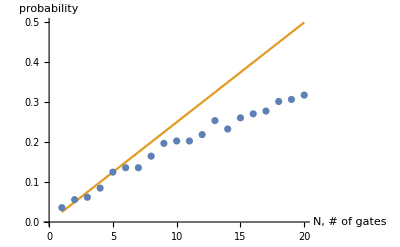

```mathematica
ListPlot[{ptable,ntable},Joined->{False,True},AxesLabel->{"N, # of gates","probability"}]
```

In the figure we plot the total probability of error (in blue) in the circuit as a function of the number of gates N. The orange line is a plot of the function f(N) = p N. We find that for N⩽ 10, the probability of error scales in direct proportion to the number of gates in the circuit. For larger values of N the curve saturates and
f(N)=N p , is an upper bound to the circuit error probability.

Exercise 1.  Explore how this graph behaves as you adjust the value of p

Exercise 2. Find the asymptotic value (i.e. as N→∞) for the circuit.

### Error for circuit containing N fault-tolerant elements.

According to the above definition of fault tolerance, the output of a fault-tolerant component has an error rate determined by the quantity c p^2 . Later, we will show that for our simple flip error c=3.

```mathematica
errorcorrectednoise[i_]:=Module[{},c=3;p=0.025;pcorr=c p^2;Which[i==1,RandomChoice[{pcorr,1-pcorr}->{0,1}],i==0,RandomChoice[{pcorr,1-pcorr}->{1,0}]]]
```

```mathematica
p1[n_]:=Module[{state=1,notstate=0},t=Table[Nest[errorcorrectednoise,state,n],{i,1,1000}];N[Count[t,notstate]/1000]]
```

```mathematica
numgates=50;
p1table=Table[{n,p1[n]},{n,1,numgates}];
n1table=Table[{n,n c p^2},{n,1,numgates}];
```

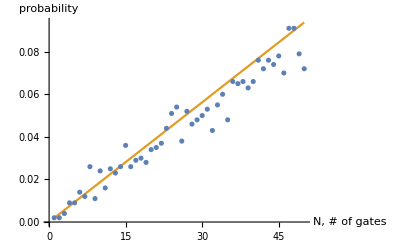

```mathematica
ListPlot[{p1table,n1table},Joined->{False,True},AxesLabel->{"N, # of gates","probability"}]
```

In this graph the solid line is now the function  g(p) = N c p^2.

This figure demonstrates that with a set of N fault tolerant gates, we can limit the circuit error probabiity to a new bound  g(p) .

Exercise 3. Plot the above graph for various values of p.

Exercise 4. Given N circuit elements, for what critical value p is g(p_c) ⩾ f(p_c) ?  If p > p_c do fault-tolerant gates provide any advantage ?

If p < p_c < 1/2, then we expect that fault tolerance allows,  for a circuit containing N elements, a fractional error bound given by the quantity N c p^2. For a maximum tolerable error ϵ

N c p^2 < ∈

This inequality limits the total number of gates allowed in the circuit. If we require more gates to complete our task, we can increase N only if the error probability p is reduced. This could be problematic as the value for p is hardware dependent. There is another way to limit the right hand side of this inequality as N increases. It is called concatenation.

### Concatenation

Before describing concatenation, lets first review a single-qubit QECC for bit flip errors. The code involves replacing the physical qubit states |0⟩, |1⟩,  with their logical qubit assignments |000⟩, and |111⟩ respectively.
After being subjected to a bit flip error they are processed by the circuit shown in Fig. 9.3 of the text. Disregarding the ancillary qubits, this circuit maps all eight possible three-qubit assignments into the space spanned by the codewords |000⟩ and |111⟩.  That is,

-Graphics-

As shown in Notebook 9.3, with this mapping the failure rate proportional to p is reduced to order c p^2, where c=3.  In second order concatenation, the manner in which  physical qubits are mapped into codewords is repeated so that the new codewords are



and which are processed in the manner described by the diagram below

-Graphics-

In this figure an initial codeword state has been corrupted by bit flip errors so that it has the form

|101⟩⊗|100⟩⊗|110⟩

Each of the three segments is then mapped according to the rules given by Eq. (1).  In the second level of processing we again apply mapping given by Eq. (1), but the intermediate state 

|111⟩⊗|000⟩⊗|111⟩

is interpreted as a codeword |1 ⟩⊗|0⟩⊗|1⟩, and according rule (1), is mapped into

|1⟩⊗|1⟩⊗|1⟩ ≡ |111⟩⊗|111⟩ ⊗|111⟩

Exercise 5.  Evaluate the output, using the mappings illustrated in Fig. (3), for the following inputs

(a) |101⟩⊗|000⟩⊗|111⟩,         (b) |100⟩⊗|000⟩⊗|111⟩       (c) |100⟩⊗|100⟩⊗|100⟩

#### Simulation of concatenated code

##### Level 0 processing

```mathematica
ClearAll["Global`*"]
(* define a bit flip error *)
bitflip[i_]:=Module[{p=0.1},prob=p;Which[i==1,RandomChoice[{p,1-p}->{0,1}],i==0,RandomChoice[{p,1-p}->{1,0}]]]
```

Create an ensemble of outputs for input state |1⟩

```mathematica
input=1;
max=10000;
ensemble0=Table[bitflip[input],{i,1,max}];
error0=(max-N[Count[ensemble0,input]])/max;
Print[" probablity of error for a single qubit flip  ",error0]
```

probablity of error for a single qubit flip  0.1004

##### Level 1 processing

Define 3-qubit mapping as determined by rule (1).

```mathematica
(* mapping rules given by Eq. (1), or Eq. 9.7 in the text *)
maprules={{0,0,0}->{0,0,0},{0,0,1}->{0,0,0},{0,1,0}->{0,0,0},{1,0,0}->{0,0,0},{0,1,1}->{1,1,1},{1,1,0}->{1,1,1},{1,0,1}->{1,1,1},{1,1,1}->{1,1,1}};
```

```mathematica
(* define codewords *)
encode1[i_]:=Which[i==0,{0,0,0},i==1,{1,1,1}]
```

Create an ensemble of outputs after level 1 QECC processing.

```mathematica
ensemble1=Table[Map[bitflip,encode1[input]] /. maprules,{i,1,max}];
zeros=Count[ensemble1,{0,0,0}];
ones=Count[ensemble1,{1,1,1}];
error1=Which[input==1,N[(max-ones)/max],input==0,N[(max-zeros)/max]];
Print[" # of Logical zeros ",zeros,"    # of Logical ones ",ones ,"     % error ",error1]
```

# of Logical zeros 271    # of Logical ones 9729     % error 0.0271

##### Level II processing

We now implement second-level encoding and processing

```mathematica
encode2[i_]:=Which[i==0,{{0,0,0},{0,0,0},{0,0,0}},i==1,{{1,1,1},{1,1,1},{1,1,1}}]
maprules2= maprules /. {0 ->{0,0,0},1->{1,1,1}}
```

{{{0,0,0},{0,0,0},{0,0,0}}→{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{1,1,1}}→{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{1,1,1},{0,0,0}}→{{0,0,0},{0,0,0},{0,0,0}},{{1,1,1},{0,0,0},{0,0,0}}→{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{1,1,1},{1,1,1}}→{{1,1,1},{1,1,1},{1,1,1}},{{1,1,1},{1,1,1},{0,0,0}}→{{1,1,1},{1,1,1},{1,1,1}},{{1,1,1},{0,0,0},{1,1,1}}→{{1,1,1},{1,1,1},{1,1,1}},{{1,1,1},{1,1,1},{1,1,1}}→{{1,1,1},{1,1,1},{1,1,1}}}

```mathematica
(* run the simulation and create an ensmeble of codewords *)
encode2[input];
ensemble2=Table[Module[{},level1=Map[bitflip,encode2[input],{2}] /. maprules;
level2=Flatten[level1 /. maprules2]],{i,1,max}];
zeros=Count[ensemble2,{0,0,0,0,0,0,0,0,0}];
ones=Count[ensemble2,{1,1,1,1,1,1,1,1,1}];
error2=Which[input==1,N[(max-ones)/max],input==0,N[(max-zeros)/max]];
Print[" # of Logical zeros ",zeros,"    # of Logical ones ",ones ,"     % error ",error2]
```

# of Logical zeros 19    # of Logical ones 9981     % error 0.0019

Exercise 6. Taking the data from these simulations, confirm that first and second order concatenation procedures did indeed results in single-qubit error probabilities that scale as c p^2, and c (c p^2)^2 respectively. Check this scaling for various values of p.

Exercise 7. Suppose we concatenate up to the kth level. Show that the probability of error scales as 
 (c p)^(2^k)/c.

### Fault Tolerance

Having established that, after the kth concatenation, of an QECC, the probability of a single bit flip error can be reduced to 
    (c p)^(2^k)/c  
We can re-write Eq. (1) as

N(c p)^(2^k) < ∈ c

and can always find a value of k, for a given N, for which this equality is satisfied. However, there is a price to pay. Each concatenation introduces additional resources (e.g. gates) . So if level 1 encoding requires d resources, second order concatenation requires d^2 resources, and kthorder concatenation requires d^kresources.

Problem 1. Using Eq. (4) demonstrate that the number of additional resources d^krequired to implement a fault tolerant  circuit with N gates and error ϵ scales as

### Upshot

The upshot of our discussion is the following. Consider a circuit that is limited by qubits that have a failure rate determined by the value for p. If a QECC can be implemented in a fault tolerant manner so that  p c <1/2, then we can always construct a concatenated circuit that satisfies inequality (4). Importantly, the extra resources required to implement that circuit only grow as a polynomial of logN

1	Phillip Kaye, Raymond Laflamme, Michele Mosca, An Introduction to Quantum Computing, pg. 235, Oxford (2007)